```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/src/nb

```mathematica
<<"IGraphM`"
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
Needs["WolframChemistry`MoleculeFingerprints`"]
```

```mathematica
<<../InputFunctions.wl
```

```mathematica
defaultBioToColor[bio_]:=Which[
bio<5,Darker@Red,
5<=bio<6,Red,
6<=bio<7,Orange,
7<=bio<8,Yellow,
8<=bio<9,Darker@Green,
9<=bio<10,LightBlue,
10<=bio,Blue,True,White]
```

```mathematica
Options[generateInput]=Join[{"BioData"->False,"BioType"->"pKi"},Options[assignFingerprintsList]];
generateInput[userInput_,opts:OptionsPattern[]]:=Module[{dataset},
dataset=Which[
StringQ[userInput]&&StringEndsQ[userInput,".csv"],If[TrueQ[OptionValue["BioData"]],generateDatasetBio[userInput,OptionValue["BioType"]],generateDataset[userInput]],
StringQ[userInput]&&StringEndsQ[userInput,".smi"],Import[userInput],
ListQ[userInput]&&moleculeListQ[userInput],userInput,
ListQ[userInput]&&validSmilesQ[First@userInput],Molecule/@userInput,
True,$Failed];
If[dataset===$Failed,Return[$Failed]];
If[ListQ[userInput],
$fingerprintDataList=assignFingerprintsList[dataset,"Fingerprint"->OptionValue["Fingerprint"]],
$fingerprintData=assignFingerprints[dataset,"Fingerprint"->OptionValue["Fingerprint"]]]
]
```

```mathematica
Options[generateGraphWithMols]=Join[Options[MoleculeDistance],{"Embedding"->"GravityEmbedding"}];
generateGraphWithMols[fingerprintData_Dataset,cutoff_,OptionsPattern[]]:=Module[{fingerprints,edges,graph},
fingerprints=KeyValueMap[{#1,#2["Fingerprint"]}&,fingerprintData]//Normal;
edges=ParallelMap[UndirectedEdge[Sequence@@First/@#]->N@*OptionValue["DistanceFunction"]@@Last/@#&,Subsets[fingerprints,{2}]]//Association;
graph=Select[edges,#<=cutoff&]//Keys//Graph[Tooltip[#,MoleculePlot[fingerprintData[#,"Molecule"]]]&/@Union@@List@@@#,#,GraphLayout->OptionValue["Embedding"]]&;
SetProperty[graph,EdgeWeight->Normal@Map[1-#&,edges]]
]
```

```mathematica
Options[generateGraph]=Join[Options[MoleculeDistance],{"Embedding"->"GravityEmbedding"}];
generateGraph[fingerprintData_Dataset,cutoff_,OptionsPattern[]]:=Module[{fingerprints,edges,graph},
fingerprints=KeyValueMap[{#1,#2["Fingerprint"]}&,fingerprintData]//Normal;
edges=ParallelMap[UndirectedEdge[Sequence@@First/@#]->N@*OptionValue["DistanceFunction"]@@Last/@#&,Subsets[fingerprints,{2}]]//Association;
graph=Select[edges,#<=cutoff&]//Keys//Graph[Tooltip/@Union@@List@@@#,#,GraphLayout->OptionValue["Embedding"]]&;
SetProperty[graph,EdgeWeight->Normal@Map[1-#&,edges]]
]
```

```mathematica
Options[chemicalSpaceNetwork]:=Join[{"Embed Molecules"->False},{"Coloring"->defaultBioToColor},Options[generateGraph],Options[generateInput]]
chemicalSpaceNetwork[userInput_,cutoff_,opts:OptionsPattern[]]:=Module[{fingerprints,vertices,style,graph,legend},
fingerprints=generateInput[userInput,"BioData"->OptionValue["BioData"],"BioType"->OptionValue["BioType"]];
graph=If[OptionValue["Embed Molecules"],generateGraphWithMols[fingerprints,cutoff],generateGraph[fingerprints,cutoff]]
(*If[OptionValue["BioData"],
vertices=VertexList[graph];
style=#->OptionValue["Coloring"][fingerprints[#,"pKi"]]&/@vertices;
legend=Row[{BarLegend[{OptionValue["Coloring"],{4,11}},6],Rotate["pKi",90Degree]}];
SetProperty[graph,VertexStyle->style]//Legended[#,legend]&,graph]*)
]
```

```mathematica
colorCommunities[graph_]:=HighlightGraph[graph,Map[Subgraph[$graph,#]&,FindGraphCommunities[graph]]]
```

```mathematica
ClearAll[$graph]
```

D5 Receptor Network

```mathematica
$graph=chemicalSpaceNetwork["../../Data/D5Activities.csv",0.5,"BioData"->True];
```

Glucocorticoid Antagonist Network - Scalfani et. al

```mathematica
$graph=chemicalSpaceNetwork["../../Data/glucocorticoid_receptor_2034_2.csv",0.42,"BioData"->True];
```

#### Cyclin Dependent Kinase Network

Full Dataset

```mathematica
$graph=chemicalSpaceNetwork["../../Data/CDKComplexData.csv",0.1,"BioData"->True,"BioType"->"IC50"];
```

Assay Format Only

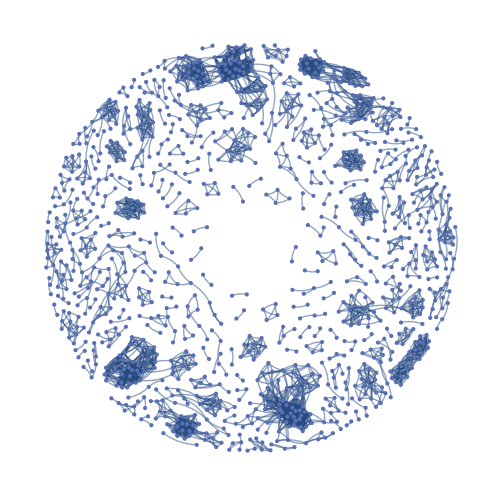

```mathematica
$graph=chemicalSpaceNetwork["../../Data/CDKDataAssays.csv",0.1,"BioData"->True,"BioType"->"IC50"]
```

```mathematica
DynamicModule[{vertexClicked={},graph=$graph,edges=EdgeList[$graph],vertices=Union@@List@@@EdgeList[$graph],clickable=False,bioData=False,bioType="pKi"},
plotLegend=Row[{BarLegend[{defualtBioToColor,{4,11}},6],Rotate[bioType,90Degree]}];
defaultVertexStyle=#->defaultBioToColor[$fingerprintData[#,bioType]]&;

Panel[
Column[{
Row[{
ActionMenu["Communities",{
"Highlight":>(graph=colorCommunities[graph]),
"Export":>Export["communities.wxf",FindGraphCommunities[graph]]
}],
ActionMenu["Connected components",{
"Highlight":>(graph=HighlightGraph[graph,ConnectedComponents[graph]]),
"Export":>Export["connectedComponents.wxf",ConnectedComponents[graph]]
}],
ActionMenu["Subgraph",{
"Generate from selected":>(graph=Subgraph[graph,vertexClicked,VertexStyle->Automatic]),
"Export":>(Export[StringJoin[{"subgraph",vertexClicked,".wxf"}],graph])
}],
ActionMenu["Adjacency Matrix",{
"Export":>(Export["graphAdjMatrix.wxf",WeightedAdjacencyMatrix[graph]]),
"Export Spectra":>(Export["adjMatrixSpectra.wxf",Eigenvalues[WeightedAdjacencyMatrix[$graph]]])
}],
ActionMenu["Switch Embedding",{
"Spring Electrical":>(graph=Annotate[graph,GraphLayout->"SpringElectricalEmbedding"])
}],
ActionMenu["Representative Molecule",{
"Show Plot":>CreateDialog[MoleculePlot[$fingerprintData[First@Part[VertexList[graph],Ordering[DegreeCentrality[graph],All,Greater]],"Molecule"]]],
"Highlight":>(graph=HighlightGraph[graph,First@Part[VertexList[graph],Ordering[DegreeCentrality[graph],All,Greater]]])
}],
ActionMenu["Reset",{
"Graph":>(graph=$graph),
"Selected":>(vertexClicked={}),
"All":>(graph=$graph;vertexClicked={})
}]
}],
Row[{
Button["Select Vertices",
clickable=Not[clickable];If[clickable,graph=Annotate[graph,VertexShapeFunction->
(EventHandler[Disk[#1,0.05],
"MouseClicked":>(If[CurrentValue["ShiftKey"],
vertexClicked=Join[vertexClicked,First@ConnectedComponents[graph,#2]];graph=Annotate[graph,VertexStyle->Thread[vertexClicked->Red]],
vertexClicked=Append[vertexClicked,#2];graph=Annotate[graph,VertexStyle->Thread[vertexClicked->Red]]]
)]&)];,
graph=Annotate[graph,VertexShapeFunction->Automatic]];],
Button["Show distances",(graph=Annotate[graph,EdgeLabels->"EdgeWeight"])],
Button["Show Molecules",
(graph=Annotate[graph,VertexShapeFunction->({pos,v,size}|->Inset[MoleculePlot[$fingerprintData[v,"Molecule"]],pos,Center,20*size])
])],
Button["Show Bio Data",bioData=True;
graph=Annotate[graph,VertexStyle->defaultVertexStyle/@vertices]//Legended[#,plotLegend]&],
Button["Draw Edge Weights",graph=graph//
IGEdgeMap[Identity,"weight"->IGEdgeProp[EdgeWeight]]/*
IGEdgeMap[Directive[AbsoluteThickness[9 #1]]&,EdgeStyle->{IGEdgeProp["weight"]}]]
}],
Panel[Dynamic[graph],Alignment->Center]
},Alignment->Center]
]
]
```